# Reproduce Robicheux 2019 Calculation for Sr87 Rydberg state

```mathematica
Clear[m,s,Coul,kg]
u = 1.66053906660*10^-27 kg;
me = 9.1093837015*10^-31 kg;
c=299792458 m/s;
ϵ0 = 8.85418782 10^-12 (s^2 Coul^2)/(m^3 kg);
ℏ=6.62607004/(2π) 10^-34 (m^2 kg)/s;
kB = 1.3806485 10^-23 kg m^2/s^2 1/Kelvin;
μB=9.274009994*10^-28 kg m^2/s^2 1/G;
a0 = 5.29 10^-11 m;
electroncharge = 1.602 10^-19 Coul;
mSr = 1.46127 10^-25 kg; (*mass of 88Sr*)
cm = .01m;mm=10^-3 m;μm=10^-6 m;nm = 10^-9 m;
THz=10^12 s^-1;GHz=10^9 s^-1;MHz=10^6 s^-1;kHz=10^3 s^-1;
mW = 10^-3 kg m/s^2 m/s;W = kg m/s^2 m/s; μW=10^-6 W;
Tesla = 10000 G;
w0813 = .776μm;
M88plus = 87.90561*u - me;
M87plus = 86.90887750*u - me;
R88 = 109737.31568160 cm^-1 *M88plus/(M88plus+me);
R87 = 109737.31568160 cm^-1 *M87plus/(M87plus+me);
ϵthr = 45932.1956 cm^-1;
Inuc = 9/2;
a5s = -1.000473673 *0.033357 cm^-1;
```

```mathematica
μ[n_, mus_] := mus[[1]] + mus[[2]]/(n-mus[[1]])^2+mus[[3]]/(n-mus[[1]])^4
Energy87[n_,mus_]:= (ϵthr -R87/(n-μ[n, mus])^2)
Energy88[n_,mus_]:= (ϵthr -R88/(n-μ[n, mus])^2)
```

## Quantum defect and energy level (Check)

```mathematica
rawQuantumDefect = Import[NotebookDirectory[]<>"Sr88QuantumDefect.csv"];
QuantumDefects = Association[StringJoin["μ's_",ToExpression[#[[1]]]]->ToExpression[{#[[2]],#[[3]],#[[4]]}]&/@ rawQuantumDefect ]
```

<|μ's_1S0→{3.26896,-0.138,0.9},μ's_3S1→{3.37078,0.418,-0.3},μ's_1P1→{2.7295,-4.67,-157},μ's_3P0→{2.8866,0.44,-1.9},μ's_3P1→{2.8824,0.407,-1.3},μ's_3P2→{2.8719,0.446,-1.9},μ's_1D2→{2.3807,-39.41,-1090},μ's_3D1→{2.67517,-13.15,-4444},μ's_3D2→{2.66142,-16.77,-6656},μ's_3D3→{2.612,-41.4,-15363},μ's_1F3→{0.089,-2,30},μ's_3F2→{0.12,2.2,120}|>

For visual check try to calculate the energy level of 88Sr from this quantum defects data.

```mathematica
lvls1S0 = Table[{(ToString[n]<>"_1S0"),Energy88[n,QuantumDefects ["μ's_1S0"]]1/cm^-1},{n,5,150}];
lvls3S1 = Table[{(ToString[n]<>"_3S1"),Energy88[n,QuantumDefects ["μ's_3S1"]]1/cm^-1},{n,5,150}];
lvls1P1 = Table[{(ToString[n]<>"_1P1"),Energy88[n,QuantumDefects ["μ's_1P1"]]1/cm^-1},{n,5,150}];
lvls3P0 = Table[{(ToString[n]<>"_3P0"),Energy88[n,QuantumDefects ["μ's_3P0"]]1/cm^-1},{n,5,150}];
lvls3P1 = Table[{(ToString[n]<>"_3P1"),Energy88[n,QuantumDefects ["μ's_3P1"]]1/cm^-1},{n,5,150}];
lvls3P2 = Table[{(ToString[n]<>"_3P2"),Energy88[n,QuantumDefects ["μ's_3P2"]]1/cm^-1},{n,5,150}];
lvls1D2 = Table[{(ToString[n]<>"_1D2"),Energy88[n,QuantumDefects ["μ's_1D2"]]1/cm^-1},{n,5,150}];
lvls3D1 = Table[{(ToString[n]<>"_3D1"),Energy88[n,QuantumDefects ["μ's_3D1"]]1/cm^-1},{n,5,150}];
lvls3D2 = Table[{(ToString[n]<>"_3D2"),Energy88[n,QuantumDefects ["μ's_3D2"]]1/cm^-1},{n,5,150}];
lvls3D3 = Table[{(ToString[n]<>"_3D3"),Energy88[n,QuantumDefects ["μ's_3D3"]]1/cm^-1},{n,5,150}];
lvls1F3 = Table[{(ToString[n]<>"_1F3"),Energy88[n,QuantumDefects ["μ's_1F3"]]1/cm^-1},{n,5,150}];
lvls3F2 = Table[{(ToString[n]<>"_3F2"),Energy88[n,QuantumDefects ["μ's_3F2"]]1/cm^-1},{n,5,150}];
```

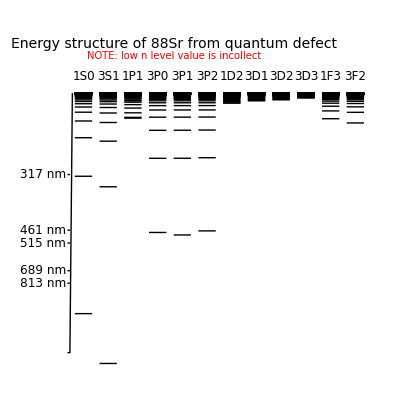

```mathematica
makeLevel[enlist_,J_]:=Line[{{J,#},{J+.7,#}}]&/@enlist[[;;,2]] ;
levelDiag = {makeLevel[lvls1S0,0],makeLevel[lvls3S1,1],makeLevel[lvls1P1,2],makeLevel[lvls3P0,3],makeLevel[lvls3P1,4],makeLevel[lvls3P2,5],makeLevel[lvls1D2,6],makeLevel[lvls3D1,7],makeLevel[lvls3D2,8],makeLevel[lvls3D3,9],makeLevel[lvls1F3,10],makeLevel[lvls3F2,11]};
labellist={"1S0","3S1","1P1","3P0","3P1","3P2","1D2","3D1","3D2","3D3","1F3","3F2"};
levelLabels =Table[ {Black,Text[Style[labellist[[ii]],"Label",12],{0.35+ii-1,50000},{0,1}]},{ii,1,Length[labellist]}];
graphicLabel={{Black,Text[Style["Energy structure of 88Sr from quantum defect","Label",14],{4,56000},{0,1}]},
{Red,Text[Style["NOTE: low n level value is incollect","Label",10],{4,53500},{0,2}]}};
scaleinfo={ToString[#]<>" nm",(# nm)^-1 cm}&/@{813,689,515, 461, 317};
graphicScale={Line[{{-.3,0},{-.2,0},{-.1,46000}}],Table[{Line[{{-.2,scaleinfo[[ii,2]]},{-.3,scaleinfo[[ii,2]]}}],Text[Style[scaleinfo[[ii,1]],12,"Label",Black],{-.35,scaleinfo[[ii,2]]},{1,0}]},{ii,1,Length[scaleinfo]}]};
levelGraphic=Graphics[{levelDiag ,graphicScale,levelLabels,graphicLabel},AspectRatio->1]
```

## Energy independent quantum defect (simpler version just for the check of calculation)

```mathematica
μ1S0n82 = μ[82, QuantumDefects ["μ's_1S0"]];
μ3S1n82 = μ[82, QuantumDefects ["μ's_3S1"]];
```

```mathematica
Kin = DiagonalMatrix[Tan/@{π μ1S0n82,π μ3S1n82,π μ3S1n82,π μ3S1n82}] ; Kin //MatrixForm
```

(1.12668 | 0. | 0. | 0.
0. | 2.32781 | 0. | 0.
0. | 0. | 2.32781 | 0.
0. | 0. | 0. | 2.32781)

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar)  √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
```

```mathematica
Minout1 =DiagonalMatrix[{InOut1[0,0,0,9/2,9/2,9/2],InOut1[1,0,1,9/2,7/2,7/2],InOut1[1,0,1,9/2,9/2,9/2],InOut1[1,0,1,9/2,11/2,11/2]}]; 
Kout1 = Transpose[Minout1].Kin.Minout1; Kout1 //MatrixForm
```

(1.12668 | 0. | 0. | 0.
0. | 2.32781 | 0. | 0.
0. | 0. | 2.32781 | 0.
0. | 0. | 0. | 2.32781)

```mathematica
Mout1out2 = {{0,Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 5],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 7/2, 4],0,
0,0},
{0,Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 5],0}
,{0,0,
0,Out1Out2[ 1/2, 1/2, 1, Inuc, 11/2, 5]}}; Mout1out2//MatrixForm
```

(0 | -3/(2 √5) | (√(11/5))/2 | 0
1 | 0 | 0 | 0
0 | (√(11/5))/2 | 3/(2 √5) | 0
0 | 0 | 0 | 1)

```mathematica
Kout2 = Transpose[Mout1out2].Kout1.Mout1out2;Kout2//MatrixForm
```

(2.32781 | 0. | 0. | 0.
0. | 1.7873 | 0.597557 | 0.
0. | 0.597557 | 1.66719 | 0.
0. | 0. | 0. | 2.32781)

```mathematica
Tanpiν2[Eb_] = FullSimplify[DiagonalMatrix[Tan[π √(R87/(# - Eb cm^-1)) ]&/@{0,0,5a5s,5a5s}]]
```

{{Tan[1040.7 √(-1/Eb)],0.,0.,0.},{0.,Tan[1040.7 √(-1/Eb)],0.,0.},{0.,0.,Tan[1040.7 √(-1/(0.166864+1. Eb))],0.},{0.,0.,0.,Tan[1040.7 √(-1/(0.166864+1. Eb))]}}

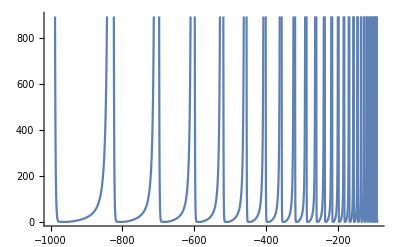

```mathematica
Plot[Det[Kout2 + Tanpiν2[Eb]]== -0.00, {Eb, -1000,-90}]
```

```mathematica
EnergyListrawA=  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -20000000<Eb<-200},{Eb},Reals] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -200<Eb<-100},{Eb},Reals] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -100<Eb<-50},{Eb},Reals] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -50<Eb<-20},{Eb},Reals] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  NSolve[{Det[Kout2 + Tanpiν2[Eb]]== 0, -20<Eb<-10},{Eb},Reals] ;
EnergyListE = Eb/.EnergyListrawB;
EnergyList = Join[EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE]
```

{-41345.4,-36620.8,-5121.09,-5121.,-5120.92,-4902.78,-3463.27,-3463.18,-3463.1,-3341.13,-2497.26,-2497.17,-2497.1,-2422.15,-1885.55,-1885.45,-1885.38,-1836.09,-1473.89,-1473.8,-1473.72,-1439.61,-1183.69,-1183.59,-1183.52,-1158.95,-971.469,-971.377,-971.302,-953.033,-811.605,-811.514,-811.438,-797.493,-688.19,-688.099,-688.023,-677.144,-590.931,-590.84,-590.764,-582.118,-512.926,-512.835,-512.759,-505.78,-449.409,-449.319,-449.242,-443.531,-397.003,-396.913,-396.836,-392.107,-353.259,-353.169,-353.093,-349.136,-316.369,-316.28,-316.203,-312.861,-284.972,-284.883,-284.806,-281.961,-258.03,-257.941,-257.863,-255.423,-234.737,-234.648,-234.57,-232.464,-214.463,-214.375,-214.296,-212.468,-196.709,-196.621,-196.542,-194.945,-181.073,-180.985,-180.906,-179.505,-167.231,-167.144,-167.064,-165.83,-154.919,-154.833,-154.752,-153.661,-143.92,-143.834,-143.753,-142.784,-134.053,-133.968,-133.886,-133.022,-125.168,-125.084,-125.001,-124.229,-117.139,-117.056,-116.972,-116.281,-109.859,-109.777,-109.692,-109.071,-103.239,-103.157,-103.072,-102.512,-97.1999,-97.1196,-97.0331,-96.5279,-91.6767,-91.5974,-91.5098,-91.0529,-86.612,-86.5338,-86.4451,-86.0309,-81.9564,-81.8794,-81.7895,-81.4134,-77.667,-77.5912,-77.5002,-77.1579,-73.7065,-73.6319,-73.5396,-73.2277,-70.0419,-69.9686,-69.875,-69.5903,-66.6446,-66.5726,-66.4777,-66.2174,-63.4891,-63.4186,-63.3223,-63.0839,-60.5531,-60.484,-60.3863,-60.1677,-57.8167,-57.749,-57.6498,-57.4491,-55.2621,-55.196,-55.0953,-54.9107,-52.8737,-52.8091,-52.7068,-52.5368,-50.6372,-50.5742,-50.4704,-50.3136,-48.5402,-48.4787,-48.3733,-48.2285,-46.5712,-46.5112,-46.4043,-46.2704,-44.72,-44.6616,-44.5531,-44.4291,-42.9774,-42.9206,-42.8105,-42.6955,-41.335,-41.2798,-41.1682,-41.0613,-39.7854,-39.7318,-39.6186,-39.5192,-38.3217,-38.2696,-38.1548,-38.0623,-36.9376,-36.8871,-36.7708,-36.6845,-35.6275,-35.5785,-35.4606,-35.3801,-34.3862,-34.3387,-34.2193,-34.144,-33.2089,-33.1629,-33.0421,-32.9716,-32.0914,-32.0467,-31.9245,-31.8585,-31.0296,-30.9863,-30.8627,-30.8008,-30.0199,-29.978,-29.853,-29.7948,-29.059,-29.0184,-28.8921,-28.8374,-28.1437,-28.1044,-27.9768,-27.9253,-27.2712,-27.2332,-27.1044,-27.0558,-26.439,-26.4022,-26.2721,-26.2262,-25.6444,-25.6088,-25.4776,-25.4343,-24.8854,-24.8509,-24.7185,-24.6776,-24.1598,-24.1264,-23.993,-23.9542,-23.4657,-23.4334,-23.2988,-23.2621,-22.8013,-22.77,-22.6344,-22.5996,-22.1649,-22.1346,-21.998,-21.965,-21.555,-21.5256,-21.3881,-21.3567,-20.97,-20.9416,-20.8032,-20.7734,-20.4088,-20.3812,-20.2419,-20.2136,-19.87,-19.8433,-19.7031,-19.6761,-19.3524,-19.3265,-19.1855,-19.1598,-18.8549,-18.8298,-18.688,-18.6636,-18.3765,-18.3522,-18.2097,-18.1863,-17.9163,-17.8927,-17.7494,-17.7272,-17.4733,-17.4504,-17.3064,-17.2852,-17.0467,-17.0244,-16.8798,-16.8595,-16.6356,-16.614,-16.4688,-16.4494,-16.2394,-16.2184,-16.0726,-16.054,-15.8573,-15.8369,-15.6905,-15.6728,-15.4887,-15.4689,-15.3219,-15.3049,-15.133,-15.1136,-14.9661,-14.9499,-14.7894,-14.7706,-14.6226,-14.6071,-14.4576,-14.4393,-14.2907,-14.2759,-14.1369,-14.1191,-13.9701,-13.9559,-13.8269,-13.8096,-13.6601,-13.6465,-13.5271,-13.5102,-13.3603,-13.3473,-13.2371,-13.2206,-13.0703,-13.0578,-12.9564,-12.9403,-12.7896,-12.7777,-12.6847,-12.6689,-12.5178,-12.5065,-12.4215,-12.4061,-12.2547,-12.2438,-12.1666,-12.1515,-11.9997,-11.9894,-11.9195,-11.9047,-11.7526,-11.7428,-11.68,-11.6654,-11.5131,-11.5037,-11.4477,-11.4334,-11.2808,-11.2719,-11.2224,-11.2083,-11.0555,-11.0471,-11.0037,-10.9899,-10.8369,-10.829,-10.7915,-10.7778,-10.6247,-10.6173,-10.5855,-10.5719,-10.4186,-10.4118,-10.3854,-10.3718,-10.2185,-10.2123,-10.191,-10.1774,-10.0241,-10.0186,-10.0021}

```mathematica
EnergyList2 = EnergyList  + ϵthr cm;
EnergyList3 = Partition[Delete[EnergyList2,{{1},{2}}],4]
EnergyLidt4 = Partition[EnergyList2,4];
```

{{40811.1,40811.2,40811.3,41029.4},{42468.9,42469.,42469.1,42591.1},{43434.9,43435.,43435.1,43510.},{44046.6,44046.7,44046.8,44096.1},{44458.3,44458.4,44458.5,44492.6},{44748.5,44748.6,44748.7,44773.2},{44960.7,44960.8,44960.9,44979.2},{45120.6,45120.7,45120.8,45134.7},{45244.,45244.1,45244.2,45255.1},{45341.3,45341.4,45341.4,45350.1},{45419.3,45419.4,45419.4,45426.4},{45482.8,45482.9,45483.,45488.7},{45535.2,45535.3,45535.4,45540.1},{45578.9,45579.,45579.1,45583.1},{45615.8,45615.9,45616.,45619.3},{45647.2,45647.3,45647.4,45650.2},{45674.2,45674.3,45674.3,45676.8},{45697.5,45697.5,45697.6,45699.7},{45717.7,45717.8,45717.9,45719.7},{45735.5,45735.6,45735.7,45737.3},{45751.1,45751.2,45751.3,45752.7},{45765.,45765.1,45765.1,45766.4},{45777.3,45777.4,45777.4,45778.5},{45788.3,45788.4,45788.4,45789.4},{45798.1,45798.2,45798.3,45799.2},{45807.,45807.1,45807.2,45808.},{45815.1,45815.1,45815.2,45815.9},{45822.3,45822.4,45822.5,45823.1},{45829.,45829.,45829.1,45829.7},{45835.,45835.1,45835.2,45835.7},{45840.5,45840.6,45840.7,45841.1},{45845.6,45845.7,45845.8,45846.2},{45850.2,45850.3,45850.4,45850.8},{45854.5,45854.6,45854.7,45855.},{45858.5,45858.6,45858.7,45859.},{45862.2,45862.2,45862.3,45862.6},{45865.6,45865.6,45865.7,45866.},{45868.7,45868.8,45868.9,45869.1},{45871.6,45871.7,45871.8,45872.},{45874.4,45874.4,45874.5,45874.7},{45876.9,45877.,45877.1,45877.3},{45879.3,45879.4,45879.5,45879.7},{45881.6,45881.6,45881.7,45881.9},{45883.7,45883.7,45883.8,45884.},{45885.6,45885.7,45885.8,45885.9},{45887.5,45887.5,45887.6,45887.8},{45889.2,45889.3,45889.4,45889.5},{45890.9,45890.9,45891.,45891.1},{45892.4,45892.5,45892.6,45892.7},{45893.9,45893.9,45894.,45894.1},{45895.3,45895.3,45895.4,45895.5},{45896.6,45896.6,45896.7,45896.8},{45897.8,45897.9,45898.,45898.1},{45899.,45899.,45899.2,45899.2},{45900.1,45900.1,45900.3,45900.3},{45901.2,45901.2,45901.3,45901.4},{45902.2,45902.2,45902.3,45902.4},{45903.1,45903.2,45903.3,45903.4},{45904.1,45904.1,45904.2,45904.3},{45904.9,45905.,45905.1,45905.1},{45905.8,45905.8,45905.9,45906.},{45906.6,45906.6,45906.7,45906.8},{45907.3,45907.3,45907.5,45907.5},{45908.,45908.1,45908.2,45908.2},{45908.7,45908.8,45908.9,45908.9},{45909.4,45909.4,45909.6,45909.6},{45910.,45910.1,45910.2,45910.2},{45910.6,45910.7,45910.8,45910.8},{45911.2,45911.3,45911.4,45911.4},{45911.8,45911.8,45912.,45912.},{45912.3,45912.4,45912.5,45912.5},{45912.8,45912.9,45913.,45913.},{45913.3,45913.4,45913.5,45913.5},{45913.8,45913.8,45914.,45914.},{45914.3,45914.3,45914.4,45914.5},{45914.7,45914.7,45914.9,45914.9},{45915.1,45915.2,45915.3,45915.3},{45915.6,45915.6,45915.7,45915.7},{45916.,45916.,45916.1,45916.1},{45916.3,45916.4,45916.5,45916.5},{45916.7,45916.7,45916.9,45916.9},{45917.1,45917.1,45917.2,45917.2},{45917.4,45917.4,45917.6,45917.6},{45917.7,45917.8,45917.9,45917.9},{45918.1,45918.1,45918.2,45918.2},{45918.4,45918.4,45918.5,45918.5},{45918.7,45918.7,45918.8,45918.8},{45919.,45919.,45919.1,45919.1},{45919.2,45919.3,45919.4,45919.4},{45919.5,45919.5,45919.7,45919.7},{45919.8,45919.8,45919.9,45920.},{45920.,45920.,45920.2,45920.2},{45920.3,45920.3,45920.4,45920.5},{45920.5,45920.5,45920.7,45920.7},{45920.7,45920.8,45920.9,45920.9},{45921.,45921.,45921.1,45921.1},{45921.2,45921.2,45921.4,45921.4},{45921.4,45921.4,45921.6,45921.6},{45921.6,45921.6,45921.8,45921.8},{45921.8,45921.8,45922.,45922.},{45922.,45922.,45922.2,45922.2}}

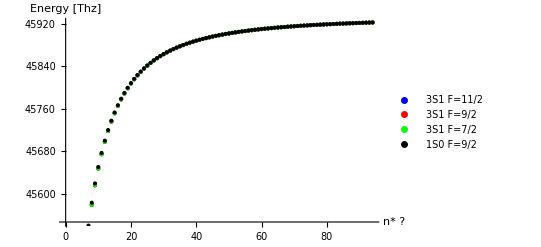

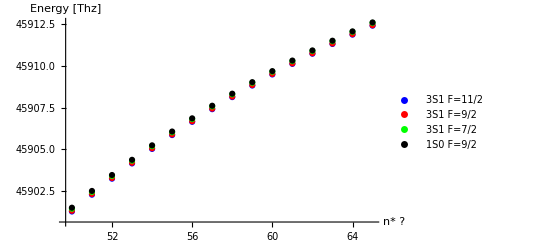

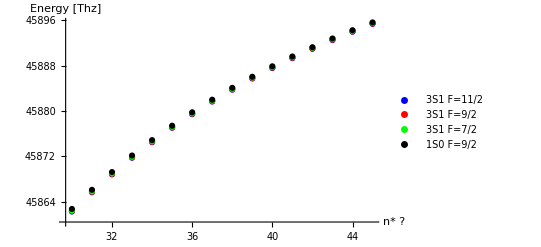

```mathematica
ListPlot[{EnergyList3[[;;,1]],EnergyList3[[;;,2]],EnergyList3[[;;,3]],EnergyList3[[;;,4]]},PlotStyle->{Blue,Red, Green,Black},PlotLegends->LineLegend[{Blue,Red, Green,Black},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListPlot[{EnergyList3[[50;;65,1]],EnergyList3[[50;;65,2]],EnergyList3[[50;;65,3]],EnergyList3[[50;;65,4]]},PlotStyle->{Blue,Red, Green,Black},PlotLegends->LineLegend[{Blue,Red, Green,Black},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"},LabelStyle->Black],DataRange->{50,65},AxesLabel->{"
n* ?","Energy [Thz]"}]
ListPlot[{EnergyList3[[30;;45,1]],EnergyList3[[30;;45,2]],EnergyList3[[30;;45,3]],EnergyList3[[30;;45,4]]},PlotStyle->{Blue,Red, Green,Black},PlotLegends->LineLegend[{Blue,Red, Green,Black},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"},LabelStyle->Black],DataRange->{30,45},AxesLabel->{"
n* ?","Energy [Thz]"}]
```

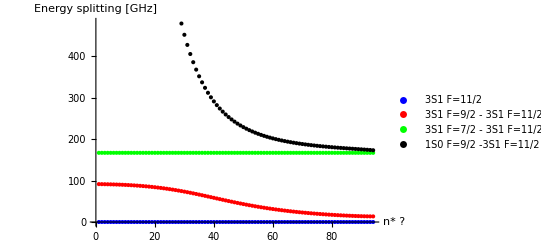

```mathematica
ListPlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]],(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*10^3,(EnergyList3[[;;,4]]-EnergyList3[[;;,1]])*10^3},PlotStyle->{Blue,Red,Green,Black},PlotLegends->LineLegend[{Blue,Red, Green,Black},{"3S1 F=11/2","3S1 F=9/2 - 3S1 F=11/2","3S1 F=7/2 - 3S1 F=11/2","1S0 F=9/2 -3S1 F=11/2"}],DataRange->{1,Length[EnergyList3[[;;,1]]]},AxesLabel->{"
n* ?","Energy splitting [GHz]"}]
```

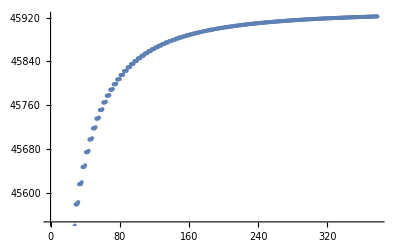

```mathematica
ListPlot[EnergyList2]
```

### Energy dependent quantum defect (Most realistic)

```mathematica
Clear[η,μenergy,Kout]
```

#### Import quantum defect

```mathematica
rawQuantumDefect = Import[NotebookDirectory[]<>"Sr88QuantumDefect.csv"];
QuantumDefects = Association[StringJoin["μ's_",ToExpression[#[[1]]]]->ToExpression[{#[[2]],#[[3]],#[[4]]}]&/@ rawQuantumDefect ]
```

<|μ's_1S0→{3.26896,-0.138,0.9},μ's_3S1→{3.37078,0.418,-0.3},μ's_1P1→{2.7295,-4.67,-157},μ's_3P0→{2.8866,0.44,-1.9},μ's_3P1→{2.8824,0.407,-1.3},μ's_3P2→{2.8719,0.446,-1.9},μ's_1D2→{2.3807,-39.41,-1090},μ's_3D1→{2.67517,-13.15,-4444},μ's_3D2→{2.66142,-16.77,-6656},μ's_3D3→{2.612,-41.4,-15363},μ's_1F3→{0.089,-2,30},μ's_3F2→{0.12,2.2,120}|>

#### Make the equation to solve

```mathematica
FullSimplify[DiagonalMatrix[Tan[π √(R87/(# - Eb cm^-1)) ]&/@{-11/20*5a5s,-11/20*5a5s,9/20*5a5s,9/20*5a5s}]]
```

{{Tan[1040.7 √(1/(0.0917752-1. Eb))],0.,0.,0.},{0.,Tan[1040.7 √(1/(0.0917752-1. Eb))],0.,0.},{0.,0.,Tan[1040.7 √(-1/(0.0750888+1. Eb))],0.},{0.,0.,0.,Tan[1040.7 √(-1/(0.0750888+1. Eb))]}}

```mathematica
Tanpiν2[Eb_] :={{Tan[1040.7002725941536 √(1/(0.09177520085321772-1. Eb))],0.,0.,0.},{0.,Tan[1040.7002725941536 √(1/(0.09177520085321772-1. Eb))],0.,0.},{0.,0.,Tan[1040.7002725941536 √(-1/(0.07508880069808724+1. Eb))],0.},{0.,0.,0.,Tan[1040.7002725941536 √(-1/(0.07508880069808724+1. Eb))]}}
```

```mathematica
R87nonUnit = R87/cm^-1;
η[Eb_]:= -Eb /R87nonUnit ;
μenergy[Eb_, mus_]:=mus[[1]]+ η[Eb]^1 mus[[2]]+η[Eb]^2 mus[[3]];
```

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar) √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
Minout1 =DiagonalMatrix[{InOut1[0,0,0,9/2,9/2,9/2],InOut1[1,0,1,9/2,7/2,7/2],InOut1[1,0,1,9/2,9/2,9/2],InOut1[1,0,1,9/2,11/2,11/2]}]; 
Mout1out2 = {{0,Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 5],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 7/2, 4],0,
0,0},
{0,Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 5],0}
,{0,0,
0,Out1Out2[ 1/2, 1/2, 1, Inuc, 11/2, 5]}}; 
Kout[Eb_]:= Transpose[Mout1out2].Transpose[Minout1].DiagonalMatrix[Tan/@{π μ1S0n82,π μ3S1n82,π μ3S1n82,π μ3S1n82}].Minout1.Mout1out2
```

#### Plot the LHS of the equation

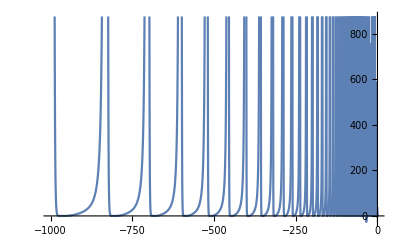

```mathematica
Plot[Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, {Eb, -1000,-0}]
```

#### Solve equation find bound energies [cm^-1]

to find the solution correctly I am using Solve on purpose. I don’t know why this goes well.

```mathematica
EnergyListrawZ=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -1000000<Eb<-5000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListZ= Eb/.EnergyListrawZ;
EnergyListrawA=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -5000<Eb<-1000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -1000<Eb<-500},{Eb},Reals, WorkingPrecision->10] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -500<Eb<-100},{Eb},Reals, WorkingPrecision->10] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0, -100<Eb<-50},{Eb},Reals, WorkingPrecision->10] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -50<Eb<-20},{Eb},Reals, WorkingPrecision->10] ;
EnergyListE = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -20<Eb<-10},{Eb},Reals, WorkingPrecision->10] ;
EnergyListF = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListZ,EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-8331.8190986146895677716,-8331.7439949723931384,-7882.910628905811559,-5120.99824308167645038751369,-5120.906498405389117431,-5120.8313790801348772,-4902.6881056290210711,-3463.1769810915138126,-3463.0852604590891312,-3463.0101170899655235,-3341.037377296682615,-2497.1715710773181021,-2497.0798846385660796,-2497.0047070757679311,-2422.0570177476795091,-1885.45459841830297471,-1885.3629581144217421,-1885.2877344167521597,-1836.0022967432901999,-1473.7955447928000206,-1473.7039643598042051,-1473.6286807912489508,-1439.518876976196291,-1183.5942413180843984,-1183.5027362912233451,-1183.42737731653321598,-1158.8600447654381983,-971.37681372603034172,-971.28540144524651077,-971.20994972447910503,-952.94096871998132583,-811.51304392467255806,-811.42174354110400002,-811.34617992312129327,-797.4007778076003999,-688.09823004318451203,-688.00706252665488515,-687.93136604163323182,-677.05183443438019904,-590.8387431486845281,-590.7477312960487828961,-590.671879147133239,-582.02648916392181351,-512.83391438332335779,-512.74308282744521748,-512.66705038177206335,-505.68800537819262122,-449.31737445864154251,-449.2267496776682906,-449.15051045709024474,-443.43949055959032756,-396.91126835722332967,-396.82087868369215894,-396.74440435567202976,-392.0153092365097237,-353.16769905886520509,-353.077574688021509801,-353.00083505731390375,-349.0438818330325525,-316.27759438430814327,-316.18776738083784792,-316.11073038275684097,-312.76926806427070169,-284.88061318274584506,-284.79111748491972919,-284.71374918119454209,-281.8688917746340576,-257.93791518312345055,-257.84878660312066388,-257.77105118157214711,-255.3312556485916828,-234.64511134597404031,-234.5563875648948337,-234.47824734442273652,-232.37209839267331289,-214.37152071215744849,-214.2832412679532999,-214.20465671060614445,-212.37577852082050486,-196.61702543484822353,-196.52923170109484904,-196.4501614332969193,-194.85356891063795848,-180.98092949399518247,-180.89366464711707135,-180.8140654924438781,-179.41350780620032544,-167.13915070921187259,-167.0524596814463551,-166.97228670766056811,-165.73828632540068597,-154.82729163639327347,-154.74122105147273077,-154.66042763484196891,-153.56881430815450005,-143.8279192375316733,-143.74251732578489045,-143.66105523598036866,-142.69185717658700429,-133.96089862143031005,-133.8762151107850499,-133.79403461987900536,-132.93063078682871344,-125.07597070396244033,-124.99205668320475249,-124.9091067024111356,-124.13757224863143213,-117.04699762893342719,-116.96390537958530391,-116.88013362738212243,-116.18872982197771261,-109.76746103151384843,-109.6852438248754309,-109.60059702996254364,-108.97937035655810326,-103.1469108449453975,-103.06562270125998132,-102.98004684339409268,-102.42051139214952694,-97.108142002775832463,-97.027837410163438724,-96.941278001224527631,-96.436161978436209623,-91.584933386276804067,-91.505666978086185254,-91.418069384725499218,-90.961111393289069951,-86.520224601017604365,-86.442050791593614089,-86.353360599466299502,-85.939144857680721249,-81.864636303823191917,-81.787608884378825401,-81.697772302271887042,-81.321594550710866519,-77.575262040372960992,-77.499433738661736445,-77.408398038821656108,-77.066155799841576407,-73.614676113151861644,-73.540098122883074976,-73.447812111600556752,-73.135914398223220789,-69.950114435076448085,-69.876835923382550562,-69.783250433525143185,-69.498543084318634986,-66.552794738051320512,-66.48086234163634399,-66.385930736500015606,-66.125634373667023234,-63.39734968641801811,-63.326807009084434819,-63.230485684866713198,-62.992143920998372988,-60.461351961965685115,-60.392239087811025719,-60.294487960414380199,-60.075923963944088887,-57.724914654418616352,-57.657267691896650867,-57.558050652867311432,-57.357330558826648458,-55.170353613478876212,-55.104204285556470049,-55.003489611927571288,-54.818891559489035785,-52.781901020827097382,-52.717276315531311233,-52.615037019275792455,-52.445024830303127978,-50.545461490896398662,-50.482383384627551429,-50.378597489345093732,-50.221798187318454436,-48.448403633812070156,-48.386888896996260006,-48.281539632260765223,-48.136724149367070442,-46.479381307932721987,-46.419441399103927319,-46.312517306381417052,-46.178583846376916533,-44.628179825434719761,-44.569820875954686695,-44.461315823883414824,-44.337275445614399824,-42.885583207841496404,-42.828806095511071824,-42.718719206290191465,-42.603683272050893495,-41.243259262035286437,-41.188059768148755553,-41.076395260483981496,-40.969564458140634351,-39.69365979417820085,-39.640028835404317605,-39.526795792626895907,-39.427450493288082005,-38.229933724859678674,-38.17785764890508403,-38.06306972330837373,-37.970561479353001362,-36.845851233823356071,-36.795312166257494114,-36.678987232272051125,-36.592731255438634291,-35.535737362648207336,-35.48671359155940153,-35.368873361096902389,-35.28834184848883736,-34.2944137512804129749,-34.246880136522842917,-34.127549749729108028,-34.0522659481874795,-33.117147389265356584,-33.071075783817306961,-32.950283387714051635,-32.879816305071858781,-31.999605432830134395,-31.954965105050704572,-31.832741431278829446,-31.766701117414517425,-30.937815280953259265,-30.894573328122894233,-30.770951279401954315,-30.708984611501689027,-29.928129222323491662,-29.886250967618274506,-29.761265220772186712,-29.703052136414422339,-28.967193064744061665,-28.926642431583598363,-28.800329063192756714,-28.745579192298445867,-28.051918242411041263,-28.012658101825141111,-27.885054240859736311,-27.833503893618820901,-27.179456967291604182,-27.141449455495040847,-27.012592965740299229,-26.964002438652649987,-26.347180050757193018,-26.310386855458582086,-26.180316049205888064,-26.134467215609739868,-25.552657072495493987,-25.517039687575610317,-25.385793070944189033,-25.342487226032387182,-24.793638617017905304,-24.759158566094448951,-24.626774615466600349,-24.585830548946457207,-24.068040335018810286,-24.034659365082622077,-23.901176333467505331,-23.862428605801858802,-23.373928618440131088,-23.341608865224806692,-23.207064616888826133,-23.170362017534073143,-22.709507705187141509,-22.678211832246956906,-22.542643703635836554,-22.507847871917231636,-22.073108052725846433,-22.042799366374103254,-21.906244051174541477,-21.8732282424458228,-21.463175839849032489,-21.433818382177472388,-21.296311838297727533,-21.264959819847617441,-20.878263473212742808,-20.849822095397166917,-20.711399471661437851,-20.681604534474035548,-20.317020990224254559,-20.289461408243254644,-20.150156988672949602,-20.121821062638852669,-19.778188262848501137,-19.751477097619062686,-19.611324261297196179,-19.584357122821323563,-19.260587918180265632,-19.234692721960244359,-19.093723916628960675,-19.068042478802053563,-18.763118901447566393,-18.738008172181710723,-18.596254899896261436,-18.571782576501652618,-18.284750615673302201,-18.260393800774698177,-18.117886614121997243,-18.094552749748774536,-17.824517579702056762,-17.800885070570114897,-17.657653578150751804,-17.635392937590019704,-17.381514552845464621,-17.35857767122807195,-17.214650551294159663,-17.193402862217850149,-16.954892080139239391,-16.932623057251644049,-16.788028078587934432,-16.767737622260852501,-16.543852417245902658,-16.522224366361567365,-16.376988415694597699,-16.357603661161873268,-16.147645798471876817,-16.126632681498342866,-15.980781796920571858,-15.962255074756988401,-15.765567015275181536,-15.745143603616327196,-15.598703013723876577,-15.580990226042537967,-15.396952276088594365,-15.377094105866598383,-15.230088274537289406,-15.213148638548737188,-15.041176321331408249,-15.021859642787311209,-14.87431231978010329,-14.85810814278850178,-14.69764977018137908,-14.678851490778449382,-14.53078576863007412,-14.515282252974560908,-14.365816678070761292,-14.347514298470405436,-14.198952676519456332,-14.184117753647810909,-14.045152285994258445,-14.027323827632398734,-13.878288284442953485,-13.864092478084329578,-13.735160944605018886,-13.71778486702826341,-13.568296943053713926,-13.554713262397625455,-13.435374197755922227,-13.41842930312425251,-13.268510196204617267,-13.255514061181698839,-13.145349011642065092,-13.128814332783844707,-12.978485010090760132,-12.966054212415694138,-12.864666137038112178,-12.848520804027703583,-12.697802135486807217,-12.685916841259569133,-12.592928593319832532,-12.577151671545743459,-12.426064591768527572,-12.414707394436372144,-12.329760264029120741,-12.314330553833602248,-12.16289626247781578,-12.152052299308322895,-12.074804594700487733,-12.059700378430379099,-11.907940593149182772,-11.897597744809542556,-11.827723384526998956,-11.812922100486446907,-11.660859382975693995,-11.651008585590072263,-11.588195664216000587,-11.573673477320894734,-11.421331662664695625,-11.411967376887942648,-11.355916653079430251,-11.341647876924146486,-11.189052651528125289,-11.180173557223787862,-11.130596789028615175,-11.116553090095415616,-10.963732787477310213,-10.955342811548123742,-10.911960825706760308,-10.898110101550594479,-10.745096824155455346,-10.737206673459918719,-10.699746991500478038,-10.686051750413058787,-10.532882989949173077,-10.525512469391471355,-10.493706205630591627,-10.480121167185157305,-10.326842204079286665,-10.320023783087882385,-10.293601346937260461,-10.280069799733862427,-10.1267373453859555,-10.120521742626871958,-10.099206571349836947,-10.085654717692639755}

#### Convert to the energy from the ground state & distribute bound energies to each state [cm^-1]

```mathematica
EnergyList = Join[EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF];
EnergyList2 = EnergyList + ϵthr cm;
EnergyList3 = Partition[EnergyList2,4] ; NumberForm[EnergyList3,10]
```

{{44960.81879,44960.9102,44960.98565,44979.25463},{45120.68256,45120.77386,45120.84942,45134.79482},{45244.09737,45244.18854,45244.26423,45255.14377},{45341.35686,45341.44787,45341.52372,45350.16911},{45419.36169,45419.45252,45419.52855,45426.50759},{45482.87823,45482.96885,45483.04509,45488.75611},{45535.28433,45535.37472,45535.4512,45540.18029},{45579.0279,45579.11803,45579.19476,45583.15172},{45615.91801,45616.00783,45616.08487,45619.42633},{45647.31499,45647.40448,45647.48185,45650.32671},{45674.25768,45674.34681,45674.42455,45676.86434},{45697.55049,45697.63921,45697.71735,45699.8235},{45717.82408,45717.91236,45717.99094,45719.81982},{45735.57857,45735.66637,45735.74544,45737.34203},{45751.21467,45751.30194,45751.38153,45752.78209},{45765.05645,45765.14314,45765.22331,45766.45731},{45777.36831,45777.45438,45777.53517,45778.62679},{45788.36768,45788.45308,45788.53454,45789.50374},{45798.2347,45798.31938,45798.40157,45799.26497},{45807.11963,45807.20354,45807.28649,45808.05803},{45815.1486,45815.23169,45815.31547,45816.00687},{45822.42814,45822.51036,45822.595,45823.21623},{45829.04869,45829.12998,45829.21555,45829.77509},{45835.08746,45835.16776,45835.25432,45835.75944},{45840.61067,45840.68993,45840.77753,45841.23449},{45845.67538,45845.75355,45845.84224,45846.25646},{45850.33096,45850.40799,45850.49783,45850.87401},{45854.62034,45854.69617,45854.7872,45855.12944},{45858.58092,45858.6555,45858.74779,45859.05969},{45862.24549,45862.31876,45862.41235,45862.69706},{45865.64281,45865.71474,45865.80967,45866.06997},{45868.79825,45868.86879,45868.96511,45869.20346},{45871.73425,45871.80336,45871.90111,45872.11968},{45874.47069,45874.53833,45874.63755,45874.83827},{45877.02525,45877.0914,45877.19211,45877.37671},{45879.4137,45879.47832,45879.58056,45879.75058},{45881.65014,45881.71322,45881.817,45881.9738},{45883.7472,45883.80871,45883.91406,45884.05888},{45885.71622,45885.77616,45885.88308,45886.01702},{45887.56742,45887.62578,45887.73428,45887.85832},{45889.31002,45889.36679,45889.47688,45889.59192},{45890.95234,45891.00754,45891.1192,45891.22604},{45892.50194,45892.55557,45892.6688,45892.76815},{45893.96567,45894.01774,45894.13253,45894.22504},{45895.34975,45895.40029,45895.51661,45895.60287},{45896.65986,45896.70889,45896.82673,45896.90726},{45897.90119,45897.94872,45898.06805,45898.14333},{45899.07845,45899.12452,45899.24532,45899.31578},{45900.19599,45900.24063,45900.36286,45900.4289},{45901.25778,45901.30103,45901.42465,45901.48662},{45902.26747,45902.30935,45902.43433,45902.49255},{45903.22841,45903.26896,45903.39527,45903.45002},{45904.14368,45904.18294,45904.31055,45904.3621},{45905.01614,45905.05415,45905.18301,45905.2316},{45905.84842,45905.88521,45906.01528,45906.06113},{45906.64294,45906.67856,45906.80981,45906.85311},{45907.40196,45907.43644,45907.56883,45907.60977},{45908.12756,45908.16094,45908.29442,45908.33317},{45908.82167,45908.85399,45908.98854,45909.02524},{45909.48609,45909.51739,45909.65296,45909.68775},{45910.12249,45910.1528,45910.28936,45910.32237},{45910.73242,45910.76178,45910.89929,45910.93064},{45911.31734,45911.34578,45911.4842,45911.514},{45911.87858,45911.90614,45912.04544,45912.07378},{45912.41741,45912.44412,45912.58428,45912.61124},{45912.93501,45912.96091,45913.10188,45913.12756},{45913.43248,45913.45759,45913.59935,45913.62382},{45913.91085,45913.93521,45914.07771,45914.10105},{45914.37108,45914.39471,45914.53795,45914.56021},{45914.81409,45914.83702,45914.98095,45915.0022},{45915.24071,45915.26298,45915.40757,45915.42786},{45915.65175,45915.67338,45915.81861,45915.838},{45916.04795,45916.06897,45916.21482,45916.23334},{45916.43003,45916.45046,45916.5969,45916.61461},{45916.79865,45916.81851,45916.96551,45916.98245},{45917.15442,45917.17374,45917.32129,45917.33749},{45917.49795,45917.51675,45917.66481,45917.68032},{45917.82978,45917.84809,45917.99665,45918.01148},{45918.15045,45918.16828,45918.31731,45918.33151},{45918.46044,45918.47782,45918.6273,45918.64089},{45918.76023,45918.77717,45918.92709,45918.94009},{45919.05025,45919.06679,45919.21711,45919.22955},{45919.33093,45919.34708,45919.4978,45919.50968},{45919.60267,45919.61845,45919.76954,45919.78089},{45919.86584,45919.88127,45920.0327,45920.04355},{45920.1208,45920.1359,45920.28766,45920.298},{45920.36788,45920.38268,45920.53474,45920.54459},{45920.6074,45920.62193,45920.77427,45920.78363},{45920.83968,45920.85395,45921.00655,45921.01543},{45921.065,45921.07905,45921.23187,45921.24026},{45921.28364,45921.29749,45921.4505,45921.45839},{45921.49585,45921.50955,45921.66272,45921.67009},{45921.70189,45921.71548,45921.86876,45921.87558},{45921.902,45921.91553,45922.06886,45922.07508}}

### Compare the result with Robicheaux 2019 paper (Succeeded to reproduce the result!!!!!!!)

(My calculation) - (Robicheaux 2019 Table 2 c result) for n=40,60,82

```mathematica
{"45850.33096","45850.40799","45850.49783","45850.87401"}-{45850.3299,45850.4070,45850.4967,45850.8743}
{"45897.90119","45897.94872","45898.06805","45898.14333"}-{45897.9011,45897.9487,45898.0680,45898.1433}
{"45914.37108","45914.39471","45914.53795","45914.56021"}-{45914.3711,45914.3947,45914.5379,45914.5602}
```

{0.0010637,0.000991116,0.0011277,-0.000294551}

{0.0000862487,0.0000198635,0.0000502503,0.0000340518}

{-0.0000175797,0.0000149294,0.0000464218,7.06241×10^-6}

#### Energy level plot

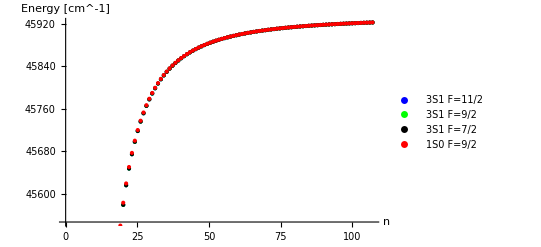

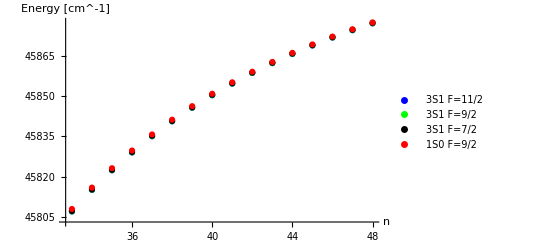

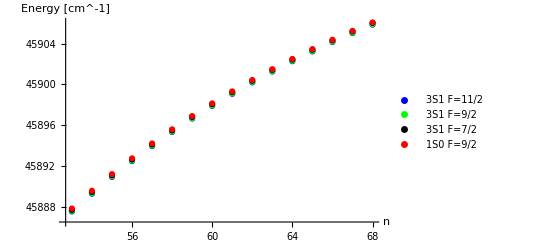

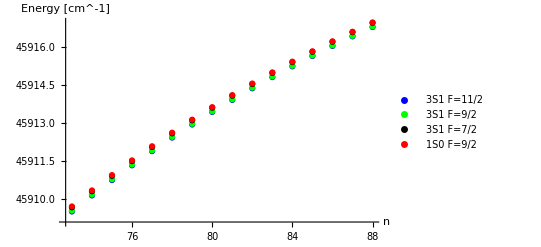

```mathematica
ListPlot[{EnergyList3[[;;,1]],EnergyList3[[;;,2]],EnergyList3[[;;,3]],EnergyList3[[;;,4]]},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"}],DataRange->{13,Length[EnergyList3[[;;,1]]]+13},AxesLabel->{"
n","Energy [cm^-1]"}]
ListPlot[{EnergyList3[[20;;35,1]],EnergyList3[[20;;35,2]],EnergyList3[[20;;35,3]],EnergyList3[[20;;35,4]]},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"},LabelStyle->Black],DataRange->{33,48},AxesLabel->{"
n","Energy [cm^-1]"}]
start = 40;
stop =55;
ListPlot[{EnergyList3[[start ;;stop,1]],EnergyList3[[start ;;stop,2]],EnergyList3[[start ;;stop,3]],EnergyList3[[start ;;stop,4]]},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"},LabelStyle->Black],DataRange->{start +13,stop+13},AxesLabel->{"
n","Energy [cm^-1]"}]
start = 60;
stop =75;
ListPlot[{EnergyList3[[start ;;stop,1]],EnergyList3[[start ;;stop,2]],EnergyList3[[start ;;stop,3]],EnergyList3[[start ;;stop,4]]},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"},LabelStyle->Black],DataRange->{start +13,stop+13},AxesLabel->{"
n","Energy [cm^-1]"}]
```

### Energy dependent quantum defect for 3P1

```mathematica
Clear[η,μenergy,Kout]
```

#### Make the equation to solve

```mathematica
FullSimplify[DiagonalMatrix[Tan[π √(R87/(# - Eb cm^-1)) ]&/@{-11/20*5a5s,-11/20*5a5s,9/20*5a5s,9/20*5a5s}]]
```

{{Tan[1040.7 √(1/(0.0917752-1. Eb))],0.,0.,0.},{0.,Tan[1040.7 √(1/(0.0917752-1. Eb))],0.,0.},{0.,0.,Tan[1040.7 √(-1/(0.0750888+1. Eb))],0.},{0.,0.,0.,Tan[1040.7 √(-1/(0.0750888+1. Eb))]}}

```mathematica
Tanpiν2[Eb_] :={{Tan[1040.7002725941536 √(1/(0.09177520085321772-1. Eb))],0.,0.,0.},{0.,Tan[1040.7002725941536 √(1/(0.09177520085321772-1. Eb))],0.,0.},{0.,0.,Tan[1040.7002725941536 √(-1/(0.07508880069808724+1. Eb))],0.},{0.,0.,0.,Tan[1040.7002725941536 √(-1/(0.07508880069808724+1. Eb))]}}
```

```mathematica
R87nonUnit = R87/cm^-1;
η[Eb_]:= -Eb /R87nonUnit ;
μenergy[Eb_, mus_]:=mus[[1]]+ η[Eb]^1 mus[[2]]+η[Eb]^2 mus[[3]];
```

```mathematica
InOut1[S_,l0_, J_, Inuc_, Ft_, Fbar_] := (-1)^(S+l0+Inuc+Ft) √((2 J +1) (2 Fbar + 1))SixJSymbol[{l0,S,J},{Inuc,Ft,Fbar}];
Out1Out2[Jc_,s0_, S_, Inuc_, Fbar_, Fc_] := (-1)^(s0+Jc+Inuc+Fbar) √((2 S +1) (2 Fc + 1))SixJSymbol[{s0,Jc,S},{Inuc,Fbar,Fc}];
(*Here I will change for l0=1!!!*)
Minout1P =DiagonalMatrix[{InOut1[0,1,0,9/2,9/2,9/2],InOut1[1,1,1,9/2,7/2,7/2],InOut1[1,1,1,9/2,9/2,9/2],InOut1[1,1,1,9/2,11/2,11/2]}]; 
Mout1out2P = {{0,Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 0, Inuc, 9/2, 5],0},
{Out1Out2[ 1/2, 1/2, 1, Inuc, 7/2, 4],0,
0,0},
{0,Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 4],
Out1Out2[ 1/2, 1/2, 1, Inuc, 9/2, 5],0}
,{0,0,
0,Out1Out2[ 1/2, 1/2, 1, Inuc, 11/2, 5]}}; 
Kout[Eb_]:= Transpose[Mout1out2P].Transpose[Minout1P].DiagonalMatrix[Tan/@{π μ1S0n82,π μ3S1n82,π μ3S1n82,π μ3S1n82}].Minout1P.Mout1out2P
```

SixJSymbol::tri: SixJSymbol[{1,0,0},{9/2,9/2,9/2}] is not triangular.

#### Plot the LHS of the equation

```mathematica
Plot[Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, {Eb, -1000,-0}]
```

-Graphics-

#### Solve equation find bound energies [cm^-1]

to find the solution correctly I am using Solve on purpose. I don’t know why this goes well.

```mathematica
EnergyListrawZ=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -1000000<Eb<-5000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListZ= Eb/.EnergyListrawZ;
EnergyListrawA=  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0.00, -5000<Eb<-1000},{Eb},Reals, WorkingPrecision->10] ;
EnergyListA = Eb/.EnergyListrawA;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -1000<Eb<-500},{Eb},Reals, WorkingPrecision->10] ;
EnergyListB = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -500<Eb<-100},{Eb},Reals, WorkingPrecision->10] ;
EnergyListC = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb]+ Tanpiν2[Eb]]== 0, -100<Eb<-50},{Eb},Reals, WorkingPrecision->10] ;
EnergyListD = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -50<Eb<-20},{Eb},Reals, WorkingPrecision->10] ;
EnergyListE = Eb/.EnergyListrawB;
EnergyListrawB =  Solve[{Det[Kout[Eb] + Tanpiν2[Eb]]== 0, -20<Eb<-10},{Eb},Reals, WorkingPrecision->10] ;
EnergyListF = Eb/.EnergyListrawB;

EnergyList = Join[EnergyListZ,EnergyListA ,EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-8331.8190986146895677716,-8331.7439949723931384,-7882.910628905811559,-5120.99824308167645038751369,-5120.906498405389117431,-5120.8313790801348772,-4902.6881056290210711,-3463.1769810915138126,-3463.0852604590891312,-3463.0101170899655235,-3341.037377296682615,-2497.1715710773181021,-2497.0798846385660796,-2497.0047070757679311,-2422.0570177476795091,-1885.45459841830297471,-1885.3629581144217421,-1885.2877344167521597,-1836.0022967432901999,-1473.7955447928000206,-1473.7039643598042051,-1473.6286807912489508,-1439.518876976196291,-1183.5942413180843984,-1183.5027362912233451,-1183.42737731653321598,-1158.8600447654381983,-971.37681372603034172,-971.28540144524651077,-971.20994972447910503,-952.94096871998132583,-811.51304392467255806,-811.42174354110400002,-811.34617992312129327,-797.4007778076003999,-688.09823004318451203,-688.00706252665488515,-687.93136604163323182,-677.05183443438019904,-590.8387431486845281,-590.7477312960487828961,-590.671879147133239,-582.02648916392181351,-512.83391438332335779,-512.74308282744521748,-512.66705038177206335,-505.68800537819262122,-449.31737445864154251,-449.2267496776682906,-449.15051045709024474,-443.43949055959032756,-396.91126835722332967,-396.82087868369215894,-396.74440435567202976,-392.0153092365097237,-353.16769905886520509,-353.077574688021509801,-353.00083505731390375,-349.0438818330325525,-316.27759438430814327,-316.18776738083784792,-316.11073038275684097,-312.76926806427070169,-284.88061318274584506,-284.79111748491972919,-284.71374918119454209,-281.8688917746340576,-257.93791518312345055,-257.84878660312066388,-257.77105118157214711,-255.3312556485916828,-234.64511134597404031,-234.5563875648948337,-234.47824734442273652,-232.37209839267331289,-214.37152071215744849,-214.2832412679532999,-214.20465671060614445,-212.37577852082050486,-196.61702543484822353,-196.52923170109484904,-196.4501614332969193,-194.85356891063795848,-180.98092949399518247,-180.89366464711707135,-180.8140654924438781,-179.41350780620032544,-167.13915070921187259,-167.0524596814463551,-166.97228670766056811,-165.73828632540068597,-154.82729163639327347,-154.74122105147273077,-154.66042763484196891,-153.56881430815450005,-143.8279192375316733,-143.74251732578489045,-143.66105523598036866,-142.69185717658700429,-133.96089862143031005,-133.8762151107850499,-133.79403461987900536,-132.93063078682871344,-125.07597070396244033,-124.99205668320475249,-124.9091067024111356,-124.13757224863143213,-117.04699762893342719,-116.96390537958530391,-116.88013362738212243,-116.18872982197771261,-109.76746103151384843,-109.6852438248754309,-109.60059702996254364,-108.97937035655810326,-103.1469108449453975,-103.06562270125998132,-102.98004684339409268,-102.42051139214952694,-97.108142002775832463,-97.027837410163438724,-96.941278001224527631,-96.436161978436209623,-91.584933386276804067,-91.505666978086185254,-91.418069384725499218,-90.961111393289069951,-86.520224601017604365,-86.442050791593614089,-86.353360599466299502,-85.939144857680721249,-81.864636303823191917,-81.787608884378825401,-81.697772302271887042,-81.321594550710866519,-77.575262040372960992,-77.499433738661736445,-77.408398038821656108,-77.066155799841576407,-73.614676113151861644,-73.540098122883074976,-73.447812111600556752,-73.135914398223220789,-69.950114435076448085,-69.876835923382550562,-69.783250433525143185,-69.498543084318634986,-66.552794738051320512,-66.48086234163634399,-66.385930736500015606,-66.125634373667023234,-63.39734968641801811,-63.326807009084434819,-63.230485684866713198,-62.992143920998372988,-60.461351961965685115,-60.392239087811025719,-60.294487960414380199,-60.075923963944088887,-57.724914654418616352,-57.657267691896650867,-57.558050652867311432,-57.357330558826648458,-55.170353613478876212,-55.104204285556470049,-55.003489611927571288,-54.818891559489035785,-52.781901020827097382,-52.717276315531311233,-52.615037019275792455,-52.445024830303127978,-50.545461490896398662,-50.482383384627551429,-50.378597489345093732,-50.221798187318454436,-48.448403633812070156,-48.386888896996260006,-48.281539632260765223,-48.136724149367070442,-46.479381307932721987,-46.419441399103927319,-46.312517306381417052,-46.178583846376916533,-44.628179825434719761,-44.569820875954686695,-44.461315823883414824,-44.337275445614399824,-42.885583207841496404,-42.828806095511071824,-42.718719206290191465,-42.603683272050893495,-41.243259262035286437,-41.188059768148755553,-41.076395260483981496,-40.969564458140634351,-39.69365979417820085,-39.640028835404317605,-39.526795792626895907,-39.427450493288082005,-38.229933724859678674,-38.17785764890508403,-38.06306972330837373,-37.970561479353001362,-36.845851233823356071,-36.795312166257494114,-36.678987232272051125,-36.592731255438634291,-35.535737362648207336,-35.48671359155940153,-35.368873361096902389,-35.28834184848883736,-34.2944137512804129749,-34.246880136522842917,-34.127549749729108028,-34.0522659481874795,-33.117147389265356584,-33.071075783817306961,-32.950283387714051635,-32.879816305071858781,-31.999605432830134395,-31.954965105050704572,-31.832741431278829446,-31.766701117414517425,-30.937815280953259265,-30.894573328122894233,-30.770951279401954315,-30.708984611501689027,-29.928129222323491662,-29.886250967618274506,-29.761265220772186712,-29.703052136414422339,-28.967193064744061665,-28.926642431583598363,-28.800329063192756714,-28.745579192298445867,-28.051918242411041263,-28.012658101825141111,-27.885054240859736311,-27.833503893618820901,-27.179456967291604182,-27.141449455495040847,-27.012592965740299229,-26.964002438652649987,-26.347180050757193018,-26.310386855458582086,-26.180316049205888064,-26.134467215609739868,-25.552657072495493987,-25.517039687575610317,-25.385793070944189033,-25.342487226032387182,-24.793638617017905304,-24.759158566094448951,-24.626774615466600349,-24.585830548946457207,-24.068040335018810286,-24.034659365082622077,-23.901176333467505331,-23.862428605801858802,-23.373928618440131088,-23.341608865224806692,-23.207064616888826133,-23.170362017534073143,-22.709507705187141509,-22.678211832246956906,-22.542643703635836554,-22.507847871917231636,-22.073108052725846433,-22.042799366374103254,-21.906244051174541477,-21.8732282424458228,-21.463175839849032489,-21.433818382177472388,-21.296311838297727533,-21.264959819847617441,-20.878263473212742808,-20.849822095397166917,-20.711399471661437851,-20.681604534474035548,-20.317020990224254559,-20.289461408243254644,-20.150156988672949602,-20.121821062638852669,-19.778188262848501137,-19.751477097619062686,-19.611324261297196179,-19.584357122821323563,-19.260587918180265632,-19.234692721960244359,-19.093723916628960675,-19.068042478802053563,-18.763118901447566393,-18.738008172181710723,-18.596254899896261436,-18.571782576501652618,-18.284750615673302201,-18.260393800774698177,-18.117886614121997243,-18.094552749748774536,-17.824517579702056762,-17.800885070570114897,-17.657653578150751804,-17.635392937590019704,-17.381514552845464621,-17.35857767122807195,-17.214650551294159663,-17.193402862217850149,-16.954892080139239391,-16.932623057251644049,-16.788028078587934432,-16.767737622260852501,-16.543852417245902658,-16.522224366361567365,-16.376988415694597699,-16.357603661161873268,-16.147645798471876817,-16.126632681498342866,-15.980781796920571858,-15.962255074756988401,-15.765567015275181536,-15.745143603616327196,-15.598703013723876577,-15.580990226042537967,-15.396952276088594365,-15.377094105866598383,-15.230088274537289406,-15.213148638548737188,-15.041176321331408249,-15.021859642787311209,-14.87431231978010329,-14.85810814278850178,-14.69764977018137908,-14.678851490778449382,-14.53078576863007412,-14.515282252974560908,-14.365816678070761292,-14.347514298470405436,-14.198952676519456332,-14.184117753647810909,-14.045152285994258445,-14.027323827632398734,-13.878288284442953485,-13.864092478084329578,-13.735160944605018886,-13.71778486702826341,-13.568296943053713926,-13.554713262397625455,-13.435374197755922227,-13.41842930312425251,-13.268510196204617267,-13.255514061181698839,-13.145349011642065092,-13.128814332783844707,-12.978485010090760132,-12.966054212415694138,-12.864666137038112178,-12.848520804027703583,-12.697802135486807217,-12.685916841259569133,-12.592928593319832532,-12.577151671545743459,-12.426064591768527572,-12.414707394436372144,-12.329760264029120741,-12.314330553833602248,-12.16289626247781578,-12.152052299308322895,-12.074804594700487733,-12.059700378430379099,-11.907940593149182772,-11.897597744809542556,-11.827723384526998956,-11.812922100486446907,-11.660859382975693995,-11.651008585590072263,-11.588195664216000587,-11.573673477320894734,-11.421331662664695625,-11.411967376887942648,-11.355916653079430251,-11.341647876924146486,-11.189052651528125289,-11.180173557223787862,-11.130596789028615175,-11.116553090095415616,-10.963732787477310213,-10.955342811548123742,-10.911960825706760308,-10.898110101550594479,-10.745096824155455346,-10.737206673459918719,-10.699746991500478038,-10.686051750413058787,-10.532882989949173077,-10.525512469391471355,-10.493706205630591627,-10.480121167185157305,-10.326842204079286665,-10.320023783087882385,-10.293601346937260461,-10.280069799733862427,-10.1267373453859555,-10.120521742626871958,-10.099206571349836947,-10.085654717692639755}

#### Convert to the energy from the ground state & distribute bound energies to each state [cm^-1]

```mathematica
EnergyList = Join[EnergyListB,EnergyListC,EnergyListD,EnergyListE,EnergyListF];
EnergyList2 = EnergyList + ϵthr cm;
EnergyList3 = Partition[EnergyList2,4] ; NumberForm[EnergyList3,10]
```

{{44960.81879,44960.9102,44960.98565,44979.25463},{45120.68256,45120.77386,45120.84942,45134.79482},{45244.09737,45244.18854,45244.26423,45255.14377},{45341.35686,45341.44787,45341.52372,45350.16911},{45419.36169,45419.45252,45419.52855,45426.50759},{45482.87823,45482.96885,45483.04509,45488.75611},{45535.28433,45535.37472,45535.4512,45540.18029},{45579.0279,45579.11803,45579.19476,45583.15172},{45615.91801,45616.00783,45616.08487,45619.42633},{45647.31499,45647.40448,45647.48185,45650.32671},{45674.25768,45674.34681,45674.42455,45676.86434},{45697.55049,45697.63921,45697.71735,45699.8235},{45717.82408,45717.91236,45717.99094,45719.81982},{45735.57857,45735.66637,45735.74544,45737.34203},{45751.21467,45751.30194,45751.38153,45752.78209},{45765.05645,45765.14314,45765.22331,45766.45731},{45777.36831,45777.45438,45777.53517,45778.62679},{45788.36768,45788.45308,45788.53454,45789.50374},{45798.2347,45798.31938,45798.40157,45799.26497},{45807.11963,45807.20354,45807.28649,45808.05803},{45815.1486,45815.23169,45815.31547,45816.00687},{45822.42814,45822.51036,45822.595,45823.21623},{45829.04869,45829.12998,45829.21555,45829.77509},{45835.08746,45835.16776,45835.25432,45835.75944},{45840.61067,45840.68993,45840.77753,45841.23449},{45845.67538,45845.75355,45845.84224,45846.25646},{45850.33096,45850.40799,45850.49783,45850.87401},{45854.62034,45854.69617,45854.7872,45855.12944},{45858.58092,45858.6555,45858.74779,45859.05969},{45862.24549,45862.31876,45862.41235,45862.69706},{45865.64281,45865.71474,45865.80967,45866.06997},{45868.79825,45868.86879,45868.96511,45869.20346},{45871.73425,45871.80336,45871.90111,45872.11968},{45874.47069,45874.53833,45874.63755,45874.83827},{45877.02525,45877.0914,45877.19211,45877.37671},{45879.4137,45879.47832,45879.58056,45879.75058},{45881.65014,45881.71322,45881.817,45881.9738},{45883.7472,45883.80871,45883.91406,45884.05888},{45885.71622,45885.77616,45885.88308,45886.01702},{45887.56742,45887.62578,45887.73428,45887.85832},{45889.31002,45889.36679,45889.47688,45889.59192},{45890.95234,45891.00754,45891.1192,45891.22604},{45892.50194,45892.55557,45892.6688,45892.76815},{45893.96567,45894.01774,45894.13253,45894.22504},{45895.34975,45895.40029,45895.51661,45895.60287},{45896.65986,45896.70889,45896.82673,45896.90726},{45897.90119,45897.94872,45898.06805,45898.14333},{45899.07845,45899.12452,45899.24532,45899.31578},{45900.19599,45900.24063,45900.36286,45900.4289},{45901.25778,45901.30103,45901.42465,45901.48662},{45902.26747,45902.30935,45902.43433,45902.49255},{45903.22841,45903.26896,45903.39527,45903.45002},{45904.14368,45904.18294,45904.31055,45904.3621},{45905.01614,45905.05415,45905.18301,45905.2316},{45905.84842,45905.88521,45906.01528,45906.06113},{45906.64294,45906.67856,45906.80981,45906.85311},{45907.40196,45907.43644,45907.56883,45907.60977},{45908.12756,45908.16094,45908.29442,45908.33317},{45908.82167,45908.85399,45908.98854,45909.02524},{45909.48609,45909.51739,45909.65296,45909.68775},{45910.12249,45910.1528,45910.28936,45910.32237},{45910.73242,45910.76178,45910.89929,45910.93064},{45911.31734,45911.34578,45911.4842,45911.514},{45911.87858,45911.90614,45912.04544,45912.07378},{45912.41741,45912.44412,45912.58428,45912.61124},{45912.93501,45912.96091,45913.10188,45913.12756},{45913.43248,45913.45759,45913.59935,45913.62382},{45913.91085,45913.93521,45914.07771,45914.10105},{45914.37108,45914.39471,45914.53795,45914.56021},{45914.81409,45914.83702,45914.98095,45915.0022},{45915.24071,45915.26298,45915.40757,45915.42786},{45915.65175,45915.67338,45915.81861,45915.838},{45916.04795,45916.06897,45916.21482,45916.23334},{45916.43003,45916.45046,45916.5969,45916.61461},{45916.79865,45916.81851,45916.96551,45916.98245},{45917.15442,45917.17374,45917.32129,45917.33749},{45917.49795,45917.51675,45917.66481,45917.68032},{45917.82978,45917.84809,45917.99665,45918.01148},{45918.15045,45918.16828,45918.31731,45918.33151},{45918.46044,45918.47782,45918.6273,45918.64089},{45918.76023,45918.77717,45918.92709,45918.94009},{45919.05025,45919.06679,45919.21711,45919.22955},{45919.33093,45919.34708,45919.4978,45919.50968},{45919.60267,45919.61845,45919.76954,45919.78089},{45919.86584,45919.88127,45920.0327,45920.04355},{45920.1208,45920.1359,45920.28766,45920.298},{45920.36788,45920.38268,45920.53474,45920.54459},{45920.6074,45920.62193,45920.77427,45920.78363},{45920.83968,45920.85395,45921.00655,45921.01543},{45921.065,45921.07905,45921.23187,45921.24026},{45921.28364,45921.29749,45921.4505,45921.45839},{45921.49585,45921.50955,45921.66272,45921.67009},{45921.70189,45921.71548,45921.86876,45921.87558},{45921.902,45921.91553,45922.06886,45922.07508}}

#### Detailed Plot of the splitting

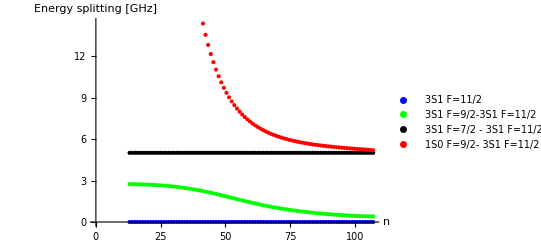

```mathematica
ListPlot[{ConstantArray[0,Length[EnergyList3[[;;,2]]]]*29.979000,(EnergyList3[[;;,2]]-EnergyList3[[;;,1]])*29.979000,(EnergyList3[[;;,3]]-EnergyList3[[;;,1]])*29.979000,(EnergyList3[[;;,4]]-EnergyList3[[;;,1]])*29.979000},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2-3S1 F=11/2","3S1 F=7/2 - 3S1 F=11/2","1S0 F=9/2- 3S1 F=11/2"}],DataRange->{13,Length[EnergyList3[[;;,1]]]+13},AxesLabel->{"
n","Energy splitting [GHz]"}]
```

### Ding 2018 (FIG.2) like plot deviation from modified 88Sr level

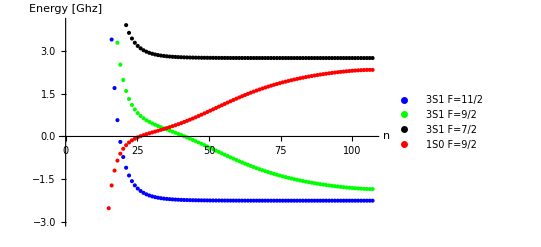

```mathematica
offset =14;
Split3s1Ip1 =EnergyList3[[;;,1]]-Table[Energy87[n,QuantumDefects ["μ's_3S1"]]1/cm^-1,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
Split3s1I1 =EnergyList3[[;;,2]]-Table[Energy87[n,QuantumDefects ["μ's_3S1"]]1/cm^-1,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
Split3s1Im1 =EnergyList3[[;;,3]]-Table[Energy87[n,QuantumDefects ["μ's_3S1"]]1/cm^-1,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
Split1s0I = EnergyList3[[;;,4]]-Table[Energy87[n,QuantumDefects ["μ's_1S0"]]1/cm^-1,{n,offset,offset-1+Length[EnergyList3[[;;,1]]]}];
ListPlot[{Split3s1Ip1 *29.979000,Split3s1I1*29.979000,Split3s1Im1*29.979000,Split1s0I*29.979000},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"}],DataRange->{13,Length[EnergyList3[[;;,1]]]+13},AxesLabel->{"
n","Energy [Ghz]"},PlotRange->{-3,4}]
```

## Search for the Foster resonance

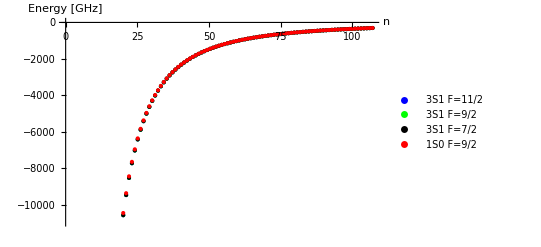

```mathematica
ListPlot[{EnergyList3[[;;,1]]*29.979000-ϵthr*cm 29.979000,EnergyList3[[;;,2]]*29.979000-ϵthr*cm 29.979000,EnergyList3[[;;,3]]*29.979000-ϵthr*cm 29.979000,EnergyList3[[;;,4]]*29.979000 -ϵthr*cm 29.979000},PlotStyle->{Blue,Green, Black,Red},PlotLegends->LineLegend[{Blue,Green, Black,Red},{"3S1 F=11/2","3S1 F=9/2","3S1 F=7/2","1S0 F=9/2"}],DataRange->{13,Length[EnergyList3[[;;,1]]]+13},AxesLabel->{"
n","Energy [GHz]"}]
```

## Calculate C6 coefficient (Not yet completed on 220208)

## Calculate the “eigen state vector” A

```mathematica
Matrix[Eb_]:=FullSimplify[(Kout[Eb]+ Tanpiν2[Eb]).DiagonalMatrix[Cos[π √(R87/(# - Eb cm^-1)) ]/(√(R87/(# - Eb cm^-1)) )^(3/2)&/@{-11/20*5a5s,-11/20*5a5s,9/20*5a5s,9/20*5a5s}]]
ACandidates=Eigensystem[Matrix[#],UpTo[4]]&/@ EnergyList;
A = Partition[ACandidates[[#,2,Ordering[Abs[ACandidates[[#,1]]],1]]][[1]]&/@Table[i,{i,Length[AunCandidates]}],4]
```

{{{0.,0.,0.,1.},{0.,0.73868,0.674056,0.},{1.,0.,0.,0.},{0.,-0.674053,0.738683,0.}},{{0.,0.,0.,1.},{0.,-0.737771,-0.675051,0.},{1.,0.,0.,0.},{0.,0.675047,-0.737774,0.}},{{0.,0.,0.,1.},{0.,0.736689,0.676231,0.},{1.,0.,0.,0.},{0.,-0.676227,0.736694,0.}},{{0.,0.,0.,1.},{0.,-0.73542,-0.677611,0.},{1.,0.,0.,0.},{0.,0.677606,-0.735425,0.}},{{0.,0.,0.,1.},{0.,0.733947,0.679207,0.},{1.,0.,0.,0.},{0.,-0.679201,0.733952,0.}},{{0.,0.,0.,1.},{0.,-0.732253,-0.681033,0.},{1.,0.,0.,0.},{0.,0.681026,-0.732259,0.}},{{0.,0.,0.,1.},{0.,0.730321,0.683104,0.},{1.,0.,0.,0.},{0.,-0.683096,0.730329,0.}},{{0.,0.,0.,1.},{0.,-0.728135,-0.685434,0.},{1.,0.,0.,0.},{0.,0.685425,-0.728143,0.}},{{0.,0.,0.,1.},{0.,0.725676,0.688037,0.},{1.,0.,0.,0.},{0.,-0.688027,0.725685,0.}},{{0.,0.,0.,1.},{0.,-0.722926,-0.690926,0.},{1.,0.,0.,0.},{0.,0.690915,-0.722936,0.}},{{0.,0.,0.,1.},{0.,0.719865,0.694114,0.},{1.,0.,0.,0.},{0.,-0.694102,0.719877,0.}},{{0.,0.,0.,1.},{0.,0.716476,0.697612,0.},{1.,0.,0.,0.},{0.,0.697599,-0.716489,0.}},{{0.,0.,0.,1.},{0.,-0.712737,-0.701431,0.},{1.,0.,0.,0.},{0.,-0.701417,0.712751,0.}},{{0.,0.,0.,1.},{0.,0.708629,0.705582,0.},{1.,0.,0.,0.},{0.,0.705566,-0.708644,0.}},{{0.,0.,0.,1.},{0.,-0.70413,-0.710071,0.},{1.,0.,0.,0.},{0.,-0.710054,0.704147,0.}},{{0.,0.,0.,1.},{0.,0.699222,0.714905,0.},{1.,0.,0.,0.},{0.,0.714887,-0.69924,0.}},{{0.,0.,0.,1.},{0.,-0.693881,-0.720089,0.},{1.,0.,0.,0.},{0.,-0.72007,0.693901,0.}},{{0.,0.,0.,1.},{0.,0.68809,0.725626,0.},{1.,0.,0.,0.},{0.,0.725605,-0.688111,0.}},{{0.,0.,0.,1.},{0.,-0.681827,-0.731514,0.},{1.,0.,0.,0.},{0.,-0.731492,0.68185,0.}},{{0.,0.,0.,1.},{0.,0.675073,0.737751,0.},{1.,0.,0.,0.},{0.,0.737727,-0.675099,0.}},{{0.,0.,0.,1.},{0.,-0.667812,-0.74433,0.},{1.,0.,0.,0.},{0.,-0.744305,0.66784,0.}},{{0.,0.,0.,1.},{0.,0.660028,0.751241,0.},{1.,0.,0.,0.},{0.,0.751215,-0.660057,0.}},{{0.,0.,0.,1.},{0.,-0.651707,-0.758471,0.},{1.,0.,0.,0.},{0.,-0.758444,0.651739,0.}},{{0.,0.,0.,1.},{0.,0.642839,0.766001,0.},{1.,0.,0.,0.},{0.,0.765972,-0.642874,0.}},{{0.,0.,0.,1.},{0.,-0.633419,-0.773809,0.},{1.,0.,0.,0.},{0.,-0.773779,0.633456,0.}},{{0.,0.,0.,1.},{0.,0.623443,0.781869,0.},{1.,0.,0.,0.},{0.,0.781837,-0.623483,0.}},{{0.,0.,0.,1.},{0.,-0.612916,-0.790148,0.},{1.,0.,0.,0.},{0.,-0.790115,0.612959,0.}},{{0.,0.,0.,1.},{0.,0.601847,0.798612,0.},{1.,0.,0.,0.},{0.,0.798577,-0.601893,0.}},{{0.,0.,0.,1.},{0.,-0.59025,-0.80722,0.},{1.,0.,0.,0.},{0.,-0.807184,0.5903,0.}},{{0.,0.,0.,1.},{0.,0.578149,0.815931,0.},{1.,0.,0.,0.},{0.,0.815894,-0.578202,0.}},{{0.,0.,0.,1.},{0.,-0.565572,-0.824699,0.},{1.,0.,0.,0.},{0.,-0.824659,0.56563,0.}},{{0.,0.,0.,1.},{0.,0.552557,0.833475,0.},{1.,0.,0.,0.},{0.,0.833434,-0.552618,0.}},{{0.,0.,0.,1.},{0.,-0.539146,-0.842212,0.},{1.,0.,0.,0.},{0.,-0.84217,0.539212,0.}},{{0.,0.,0.,1.},{0.,0.52539,0.850862,0.},{1.,0.,0.,0.},{0.,0.850818,-0.525461,0.}},{{0.,0.,0.,1.},{0.,-0.511344,-0.859376,0.},{1.,0.,0.,0.},{0.,-0.85933,0.511421,0.}},{{0.,0.,0.,1.},{0.,0.497069,0.867711,0.},{1.,0.,0.,0.},{0.,0.867664,-0.497152,0.}},{{0.,0.,0.,1.},{0.,-0.482629,-0.875825,0.},{1.,0.,0.,0.},{0.,-0.875776,0.482718,0.}},{{0.,0.,0.,1.},{0.,0.468089,0.883681,0.},{1.,0.,0.,0.},{0.,0.88363,-0.468185,0.}},{{0.,0.,0.,1.},{0.,-0.453518,-0.891247,0.},{1.,0.,0.,0.},{0.,-0.891194,0.453622,0.}},{{0.,0.,0.,1.},{0.,0.43898,0.898497,0.},{1.,0.,0.,0.},{0.,0.898442,-0.439092,0.}},{{0.,0.,0.,1.},{0.,-0.424541,-0.905409,0.},{1.,0.,0.,0.},{0.,-0.905352,0.424662,0.}},{{0.,0.,0.,1.},{0.,0.410261,0.911968,0.},{1.,0.,0.,0.},{0.,0.911909,-0.410392,0.}},{{0.,0.,0.,1.},{0.,-0.396197,-0.918166,0.},{1.,0.,0.,0.},{0.,-0.918105,0.396338,0.}},{{0.,0.,0.,1.},{0.,0.382399,0.923997,0.},{1.,0.,0.,0.},{0.,0.923934,-0.382552,0.}},{{0.,0.,0.,1.},{0.,-0.368913,-0.929464,0.},{1.,0.,0.,0.},{0.,-0.929398,0.369079,0.}},{{0.,0.,0.,1.},{0.,0.35578,0.93457,0.},{1.,0.,0.,0.},{0.,0.934502,-0.355959,0.}},{{0.,0.,0.,1.},{0.,-0.343031,-0.939324,0.},{1.,0.,0.,0.},{0.,-0.939253,0.343224,0.}},{{0.,0.,0.,1.},{0.,0.330694,0.943738,0.},{1.,0.,0.,0.},{0.,0.943665,-0.330904,0.}},{{0.,0.,0.,1.},{0.,-0.318791,-0.947825,0.},{1.,0.,0.,0.},{0.,-0.947749,0.319018,0.}},{{0.,0.,0.,1.},{0.,0.307337,0.951601,0.},{1.,0.,0.,0.},{0.,0.951521,-0.307583,0.}},{{0.,0.,0.,1.},{0.,-0.296343,-0.955082,0.},{1.,0.,0.,0.},{0.,-0.954999,0.296609,0.}},{{0.,0.,0.,1.},{0.,0.285816,0.958285,0.},{1.,0.,0.,0.},{0.,0.958199,-0.286104,0.}},{{0.,0.,0.,1.},{0.,-0.275758,-0.961227,0.},{1.,0.,0.,0.},{0.,-0.961138,0.27607,0.}},{{0.,0.,0.,1.},{0.,0.266168,0.963927,0.},{1.,0.,0.,0.},{0.,0.963833,-0.266506,0.}},{{0.,0.,0.,1.},{0.,-0.257044,-0.9664,0.},{1.,0.,0.,0.},{0.,-0.966302,0.25741,0.}},{{0.,0.,0.,1.},{0.,0.248378,0.968663,0.},{1.,0.,0.,0.},{0.,0.968561,-0.248775,0.}},{{0.,0.,0.,1.},{0.,-0.240165,-0.970732,0.},{1.,0.,0.,0.},{0.,-0.970626,0.240595,0.}},{{0.,0.,0.,1.},{0.,0.232394,0.972622,0.},{1.,0.,0.,0.},{0.,0.97251,-0.232861,0.}},{{0.,0.,0.,1.},{0.,-0.225057,-0.974346,0.},{1.,0.,0.,0.},{0.,-0.974229,0.225563,0.}},{{0.,0.,0.,1.},{0.,0.218143,0.975917,0.},{1.,0.,0.,0.},{0.,0.975794,-0.218691,0.}},{{0.,0.,0.,1.},{0.,-0.211641,-0.977347,0.},{1.,0.,0.,0.},{0.,-0.977219,0.212236,0.}},{{0.,0.,0.,1.},{0.,0.205541,0.978648,0.},{1.,0.,0.,0.},{0.,0.978513,-0.206186,0.}},{{0.,0.,0.,1.},{0.,-0.199833,-0.97983,0.},{1.,0.,0.,0.},{0.,-0.979687,0.200533,0.}},{{0.,0.,0.,1.},{0.,0.194506,0.980901,0.},{1.,0.,0.,0.},{0.,0.98075,-0.195267,0.}},{{0.,0.,0.,1.},{0.,-0.189552,-0.981871,0.},{1.,0.,0.,0.},{0.,-0.981711,0.19038,0.}},{{0.,0.,0.,1.},{0.,0.184963,0.982746,0.},{1.,0.,0.,0.},{0.,0.982576,-0.185863,0.}},{{0.,0.,0.,1.},{0.,-0.18073,-0.983533,0.},{1.,0.,0.,0.},{0.,-0.983352,0.18171,0.}},{{0.,0.,0.,1.},{0.,0.176849,0.984238,0.},{1.,0.,0.,0.},{0.,0.984046,-0.177916,0.}},{{0.,0.,0.,1.},{0.,-0.173314,-0.984867,0.},{1.,0.,0.,0.},{0.,-0.984661,0.174478,0.}},{{0.,0.,0.,1.},{0.,0.170122,0.985423,0.},{1.,0.,0.,0.},{0.,0.985203,-0.171393,0.}},{{0.,0.,0.,1.},{0.,-0.167271,-0.985911,0.},{1.,0.,0.,0.},{0.,-0.985674,0.168662,0.}},{{0.,0.,0.,1.},{0.,0.164762,0.986333,0.},{1.,0.,0.,0.},{0.,0.986078,-0.166285,0.}},{{0.,0.,0.,1.},{0.,-0.162598,-0.986692,0.},{1.,0.,0.,0.},{0.,-0.986416,0.164269,0.}},{{0.,0.,0.,1.},{0.,0.160784,0.98699,0.},{1.,0.,0.,0.},{0.,0.986689,-0.162619,0.}},{{0.,0.,0.,1.},{0.,-0.159327,-0.987226,0.},{1.,0.,0.,0.},{0.,-0.986898,0.161348,0.}},{{0.,0.,0.,1.},{0.,0.15824,0.987401,0.},{1.,0.,0.,0.},{0.,0.987041,-0.160469,0.}},{{0.,0.,0.,1.},{0.,-0.157536,-0.987513,0.},{1.,0.,0.,0.},{0.,-0.987117,0.160003,0.}},{{0.,0.,0.,1.},{0.,0.157236,0.987561,0.},{1.,0.,0.,0.},{0.,0.987122,-0.159972,0.}},{{0.,0.,0.,1.},{0.,-0.157364,-0.987541,0.},{1.,0.,0.,0.},{0.,-0.987051,0.160409,0.}},{{0.,0.,0.,1.},{0.,0.157953,0.987447,0.},{1.,0.,0.,0.},{0.,0.986897,-0.161352,0.}},{{0.,0.,0.,1.},{0.,-0.159041,-0.987272,0.},{1.,0.,0.,0.},{0.,-0.986651,0.16285,0.}},{{0.,0.,0.,1.},{0.,0.160679,0.987007,0.},{1.,0.,0.,0.},{0.,0.9863,-0.164965,0.}},{{0.,0.,0.,1.},{0.,-0.162926,-0.986638,0.},{1.,0.,0.,0.},{0.,-0.985826,0.167771,0.}},{{0.,0.,0.,1.},{0.,0.165861,0.986149,0.},{1.,0.,0.,0.},{0.,0.985208,-0.171365,0.}},{{0.,0.,0.,1.},{0.,-0.169578,-0.985517,0.},{1.,0.,0.,0.},{0.,-0.984414,0.175869,0.}},{{0.,0.,0.,1.},{0.,0.1742,0.98471,0.},{1.,0.,0.,0.},{0.,0.983403,-0.181434,0.}},{{0.,0.,0.,1.},{0.,-0.17988,-0.983689,0.},{1.,0.,0.,0.},{0.,-0.982119,0.188259,0.}},{{0.,0.,0.,1.},{0.,0.186816,0.982395,0.},{1.,0.,0.,0.},{0.,0.980484,-0.1966,0.}},{{0.,0.,0.,1.},{0.,-0.195264,-0.980751,0.},{1.,0.,0.,0.},{0.,-0.978385,0.206791,0.}},{{0.,0.,0.,1.},{0.,0.20556,0.978645,0.},{1.,0.,0.,0.},{0.,0.975662,-0.21928,0.}},{{0.,0.,0.,1.},{0.,-0.21815,-0.975915,0.},{1.,0.,0.,0.},{0.,-0.972076,0.234665,0.}},{{0.,0.,0.,1.},{0.,0.233634,0.972325,0.},{1.,0.,0.,0.},{0.,0.967266,-0.253766,0.}},{{0.,0.,0.,1.},{0.,-0.252831,-0.96751,0.},{1.,0.,0.,0.},{0.,-0.960666,0.277706,0.}},{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ},{0.,0.276866,0.960909,0.},{1.,0.,0.,0.},{0.,0.951374,-0.308037,0.}}}

## Angular component

```mathematica
PhiYPhi[FT1_,FT2_,MT1_,MT2_,  l1_, l2_, k_,q_, Fbar_] := (-1)^(2FT1-MT1+Fbar+l1+l2+k) √((2 FT1 +1) (2 FT2 + 1)(2 l1 + 1)(2 l2 +1) (2 k + 1))ThreeJSymbol[{FT1,-MT1},{k,q},{FT2,MT2}]ThreeJSymbol[{l1,0},{k,0},{l2,0}]SixJSymbol[{l1,FT1,Fbar},{FT2,l2,k}];
```

## Radial integral

```mathematica
P[ν_,l_,r_]:= (CoulombF[l,1/√ν,r√ν/a0] Cos[π (ν-l)] + CoulombG[l,1/√ν,r√ν/a0] Sin[π (ν-l)])/ν^3;
R[k_, ν1_,l1_,ν2_,l2_]:= Integrate[r^k P[ν1,l1,r] P[ν2,l2,r],{r,0,Infinity}]
```

## Calculate Q

```mathematica
SPhiYPhi[k_,q_,MT1_,MT2_,n1_,n2_] := DiagonalMatrix[{PhiYPhi[11/2,11/2,MT1,MT2,  0, 0, k,q, 11/2]*R[k, √(R87/(-11/20*5a5s - EnergyList3[[n1]] cm^-1)),0,√(R87/(-11/20*5a5s - EnergyList3[[n2]] cm^-1)),0],PhiYPhi[9/2,9/2,MT1,MT2,  0, 0, k,q, 9/2]*R[k, √(R87/(-11/20*5a5s - EnergyList3[[n1]] cm^-1)),0,√(R87/(-11/20*5a5s - EnergyList3[[n2]] cm^-1)),0],PhiYPhi[7/2,7/2,MT1,MT2,  0, 0, k,q, 7/2]*R[k, √(R87/(-11/20*5a5s - EnergyList3[[n1]] cm^-1)),0,√(R87/(9/20*5a5s- EnergyList3[[n2]] cm^-1)),0],PhiYPhi[9/2,9/2,MT1,MT2,  0, 0, k,q, 9/2]*R[k, √(R87/(-11/20*5a5s - EnergyList3[[n1]] cm^-1)),0,√(R87/(9/20*5a5s- EnergyList3[[n2]] cm^-1)),0]}]
```

```mathematica
Q1p1[n1_,n2_]:= Transpose[A[[n1]]].SPhiYPhi[1,1,MT1,MT2,n1,n2].A[[n2]];
Q1m1[n1_,n2_]:= Transpose[A[[n1]]].SPhiYPhi[1,-1,MT1,MT2,n1,n2].A[[n2]];
Q10[n1_,n2_]:= Transpose[A[[n1]]].SPhiYPhi[1,0,MT1,MT2,n1,n2].A[[n2]];
```

```mathematica
C3[n11_,n12_,n21_,n22_] := (-4π)/3(Q1p1[n11,n21]*Q1m1[n12,n22]+2Q10 [n11,n21]*Q10[n12,n22]+Q1m1[n11,n21]*Q1p1[n12,n22])
```

```mathematica
C6[n_] := Sum[(C3[n,n,n1,n2]C3[n1,n2,n,n])/(EnergyList3[[n]]-EnergyList3[[n1]]-EnergyList3[[n2]]),{{n1,1, Length[EnergyList3]},{n2,1, Length[EnergyList3]}}]
```